### Standard Definitions

```mathematica
ϕ[x_]:=If[Abs[x]>1,0,1-Abs[x]]
ϕ[l_,i_]:=(ϕ[2^l(#-2^-l(2i-1))]&)
ceil[x_]:=1+Floor[x]

test[x_]:=Sin[Pi x]^2
```

```mathematica
getCoefficient[f_,x_?NumericQ,l_]:=f[x]-1/2 f[x+2^-l]-1/2 f[x-2^-l]
fullCoefficients[f_,l_]:={{f[1],f[0]}}~Append~Table[Table[getCoefficient[f,2^-k i,k],{i,1,2^k-1,2}],{k,1,l}]
Reconstruct[coefficients_]:=If[#==1,coefficients[[1,1]],
coefficients[[1,1]]#+coefficients[[1,2]](1-#)+Sum[coefficients[[2,l,ceil[2^(l-1)#]]] ϕ[2^l(#-2^-l(2ceil[2^(l-1)#]-1))],{l,1,Length[coefficients[[2]]]}]]&

project[f_,l_]:=Reconstruct[fullCoefficients[f,l]]
```

### Standard Definitions 2D

```mathematica
test2D[x_,y_]:=Sin[Pi x]^2Sin[Pi y]^2
```

```mathematica
getCoefficient2D[f_,x_?NumericQ,y_?NumericQ,lx_,ly_]:=f[x,y]-1/2 f[x+2^-lx,y]-1/2 f[x-2^-lx,y]-1/2 f[x,y+2^-ly]-1/2 f[x,y-2^-ly]+1/4 f[x+2^-lx,y+2^-ly]+1/4 f[x-2^-lx,y+2^-ly]+1/4 f[x+2^-lx,y-2^-ly]+1/4 f[x-2^-lx,y-2^-ly]

fullCoefficients2D[f_,lx_,ly_]:=Table[Table[getCoefficient2D[f,2^-kx i,2^-ky j,kx,ky],{i,1,2^kx-1,2},{j,1,2^ky-1,2}],{kx,1,lx},{ky,1,ly}]

Reconstruct2D[coefficients_]:= If[#1==1||#2==1,0,Sum[coefficients[[lx,ly,ceil[2^(lx-1)#1],ceil[2^(ly-1)#2]]] ϕ[2^lx(#1-2^-lx(2ceil[2^(lx-1)#1]-1))] ϕ[2^ly(#2-2^-ly(2ceil[2^(ly-1)#2]-1))],{lx,1,Length[coefficients]},{ly,1,Length[coefficients[[lx]]]}]]&

project2D[f_,lx_,ly_]:=Reconstruct2D[fullCoefficients2D[f//N,lx,ly]]
```

### Example Plot

```mathematica
Plot3D[{test2D[x,y],#[x,y]},{x,0,1},{y,0,1},PlotStyle->{Opacity[.17],Opacity[1]}]&[project2D[test2D,4,4]]
```

-Graphics3D-

### Error Plot

-Graphics3D-

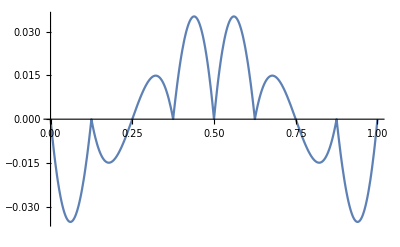

```mathematica
Plot3D[{test2D[x,y]-#[x,y]},{x,0,1},{y,0,1}]&[project2D[test2D,3,3]]
Plot[{test[x]-#[x]},{x,0,1}]&[project[test,3]]
```

### Sparse Grids

```mathematica
sparseCoefficients2D[f_,n_]:=Table[Table[Table[getCoefficient2D[f,2^-row i,2^(-(diag-row+1)) j,row,(diag-row+1)],{i,1,2^row-1,2},{j,1,2^(diag-row+1)-1,2}],{row,1,diag}],{diag,1,n}]
sparseReconstruct2[coefficients_]:=Sum[Sum[Sum[coefficients[[diag,row,i,j]] ϕ[2^row(#1-2^-row(2i-1))] ϕ[2^(diag-row+1)(#2-2^(-(diag-row+1))(2j-1))],{i,1,Length[coefficients[[diag,row]]]},{j,1,Length[coefficients[[diag,row,i]]]}],{row,1,Length[coefficients[[diag]]]}],{diag,1,Length[coefficients]}]&

sparseReconstruct[coefficients_]:=If[#1==1||#2==1,0,Sum[Sum[coefficients[[diag,row,ceil[2^(row-1)#1],ceil[2^(diag-row)#2]]] ϕ[2^row(#1-2^-row(2ceil[2^(row-1)#1]-1))] ϕ[2^(diag-row+1)(#2-2^(-(diag-row+1))(2ceil[2^(diag-row)#2]-1))],{row,1,Length[coefficients[[diag]]]}],{diag,1,Length[coefficients]}]]&

sparseProject[f_,n_]:=sparseReconstruct[sparseCoefficients2D[f,n]]
sparseProject2[f_,n_]:=sparseReconstruct2[sparseCoefficients2D[f,n]]
```

### Times to Reconstruct & Plot

```mathematica
N[sparseCoefficients2D[test2D,3]];
N[fullCoefficients2D[test2D,3,3]];
```

```mathematica
sparseReconstruct[N[sparseCoefficients2D[test2D,3]]];
Reconstruct2D[N[fullCoefficients2D[test2D,3,3]]];
```

```mathematica
Timing[Plot3D[#[x,y],{x,0,1},{y,0,1}]&[sparseProject[test2D,4]]]
Timing[Plot3D[#[x,y],{x,0,1},{y,0,1}]&[sparseProject[test2D,5]]]
```

{0.956046,-Graphics3D-}

{1.16982,-Graphics3D-}

### Error:

```mathematica
Timing[sparseError=Table[Sqrt[NIntegrate[(test2D[x,y]-#[x,y])^2,{x,0,1},{y,0,1},PrecisionGoal-> 2]&@sparseProject[test2D,n]],{n,1,4}]]
```

{16.511,{0.0698429,0.0698429,0.020768,0.00862004}}

```mathematica
sparseError={0.06987824030957586,0.06987824030957586,0.020748461191332192,0.008611605383610048,0.0030947609209268055,0.0010173120528574348,0.00031634536853842167};
```

```mathematica
error2D=Table[Sqrt[NIntegrate[(test2D[x,y]-#[x,y])^2,{x,0,1},{y,0,1},PrecisionGoal->2]&[project2D[test2D,n,n]]],{n,1,5}];
```

```mathematica
error2D={0.06987820111321434,0.06987820111321434,0.01894850318843759,0.004837982333071141,0.001215938454790851,0.000304284,0.00007609618642003117,0.00001902562886089752,4.756506114660874*^-6,1.1899116876059343025*^-6};
```

```mathematica
Table[Sqrt[(.005)^2 Sum[(test2D[x,y]-#[x,y])^2,{x,0,1,.005},{y,0,1,.005}]&@project2D[test2D,n,n]]//N,{n,1,6}]
```

$Aborted

```mathematica
Sqrt[(.01)^2 Sum[(test2D[x,y]-#[x,y])^2,{x,0,1,.01},{y,0,1,.005}]&@project2D[test2D,10,10]]
```

1.68169×10^-6

Sparse error for higher size meshes

```mathematica
sparseError2={0.06983599099420043,0.06983599099420043,0.02067656641074751,0.00850404071074545,0.003094623762907115,0.0010184013678607225,0.000316375009536311,0.00009471130522492352,0.00002758529308337097,7.875256548968977*^-6,2.2133737928888358*^-6,6.148544615513304*^-7,1.6925349250320935*^-7,4.617054711592607*^-8,1.2535491500634738*^-8,3.382568879936559*^-9}
```

{0.069836,0.069836,0.0206766,0.00850404,0.00309462,0.0010184,0.000316375,0.0000947113,0.0000275853,7.87526×10^-6,2.21337×10^-6,6.14854×10^-7,1.69253×10^-7,4.61705×10^-8,1.25355×10^-8,3.38257×10^-9}

Finding the error for a mesh at level 15, for example:

```mathematica
Sqrt[(.005)^2 Sum[(test2D[x,y]-#[x,y])^2,{x,0,1,.005},{y,0,1,.005}]&@sparseProject[test2D,15]]//N
```

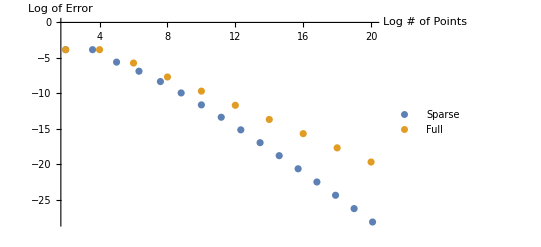

```mathematica
ListPlot[{
Table[{(*Length[Flatten[sparseCoefficients2D[test2D,n]]]//Log2*)n+Log2[n+1],sparseError2[[n]]//Log2},{n,1,16}],Table[{(*Length[Flatten[fullCoefficients2D[test2D,n,n]]]//Log2*) 2n,error2D[[n]]//Log2},{n,1,10}]}
,PlotRange->All,AxesLabel->{"Log # of Points", "Log of Error"},PlotLegends->{"Sparse","Full"}]
```

As you said, the sparse grids obtain a faster decay than the full, approaching slope -2 rather than -1. This isn’t obvious at the very beginning, and the reason is because there is a log factor that for small n will slow convergence speed.

```mathematica
LinearModelFit[Table[{(*Length[Flatten[fullCoefficients2D[test2D,n,n]]]//Log2*)2n,error2D[[n]]//Log2},{n,3,10}],x,x]
LinearModelFit[Table[{(*Length[Flatten[sparseCoefficients2D[test2D,n]]]//Log2*)n,sparseError2[[n]]//Log2},{n,15,16}],x,x]
```

FittedModel[0.285365-0.997961 x]

FittedModel[2.098-1.88983 x]

The full-grid slope will approach -1. The sparse slope will in approach -2. Although it is clear that the full grid’s slope is basically 1. The sparse grid’s error slope is not quite there yet, even at 2^20 points. We can see how the slope of the error is slowly approaching 2:

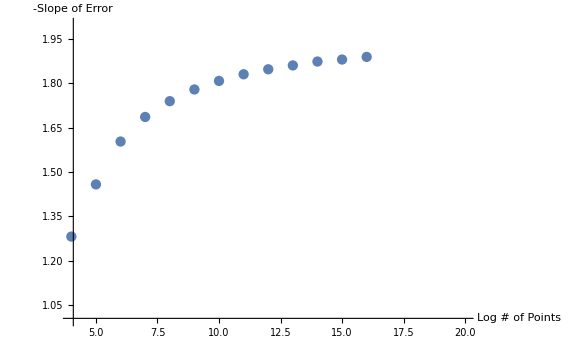

```mathematica
Show[ListPlot[{
Table[{n,-(Log2[sparseError2[[n]]]-Log2[sparseError2[[n-1]]])},{n,4,16}]}
,PlotRange->{{4,20},{1,2}},AxesLabel->{"Log # of Points", "-Slope of Error"}]]
```

Using statistical analysis, we can plot the reciprocal distance between c and the slope of the log of the error, aginst the number of points, and see that it is a linear function only at c=2. 

This is what we want, otherwise we have a vertical or horizontal asymptote, which means that the difference of the logs of the errors either equals c at a finite value of n (vertical asymptote), or never equals c (horizontal asymptote). When c = 2, the fact that the function is linear means that we hit 2 exactly at n = ∞

```mathematica
Animate[Show[ListPlot[{
Table[{n,1/(c+(Log2[sparseError2[[n]]]-Log2[sparseError2[[n-1]]]))},{n,4,16}]},PlotRange->{0,10}],Graphics[Text[Style[c,FontSize->14,Bold,FontFamily->"Times"],{10,2}]]],{c,1.9,2.1},AnimationRunning->False]
```